# Figure 2A, Supplementary Table S4B

```mathematica
Clear["Global`*"]
```

```mathematica
data=Import[NotebookDirectory[]<>"larotrectinib integrated response data.xlsx","XLSX"]⟦1⟧;
```

```mathematica
data⟦1;;10⟧//TableForm
```

Volume change (%) | Tumor type
12. | Appendix tumor
1. | Bone sarcoma
-60. | Bone sarcoma
44. | Breast tumor
24. | Cholangiocarcinoma
-78. | Cholangiocarcinoma
-22. | Colon tumor
-86. | Colon tumor
-21. | Colon tumor

## analysis of all tumor types

```mathematica
AllVolumeChangeMeasurements=data⟦2;;,1⟧;
```

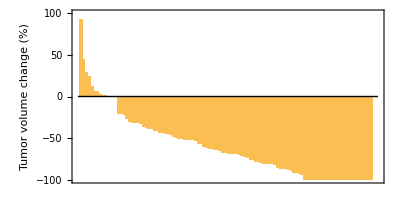

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},FrameLabel->{,"Tumor volume change (%)"},ImageSize->{{1000},{200}},AspectRatio->1/2]
```

```mathematica
RandomSamplePlot[samplesize_]:=BarChart[Reverse[Sort[RandomSample[Reverse[Sort[AllVolumeChangeMeasurements]],samplesize]]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},(*FrameLabel->{,"Tumor volume change (%)"},*)AspectRatio->4,ImageSize->{{1000},{200}},ChartStyle->EdgeForm[None]]
```

```mathematica
VolumeChangeMeasurementsAndTumorType=data⟦2;;,{2,1}(* swapped column order compared to neratinib analysis *)⟧;
```

```mathematica
TumorTypes=Sort[Tally[data⟦2;;,2⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Soft tissue sarcoma | 25
Salivary-gland tumor | 18
Infantile fibrosarcoma | 16
Thyroid tumor | 15
Lung tumor | 7
Melanoma | 5
Gastrointestinal stromal tumor | 5
Colon tumor | 5
Unknown primary | 3
Cholangiocarcinoma | 2
Bone sarcoma | 2
Pancreatic tumor | 1
Congenital mesoblastic nephroma | 1
Breast tumor | 1
Appendix tumor | 1

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]//N},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
MedianResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Median[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]//N},{i,1,Length[TumorTypes]}];
MedianResponsePerTumorType//TableForm
```

Soft tissue sarcoma | -63.
Salivary-gland tumor | -59.2222
Infantile fibrosarcoma | -83.375
Thyroid tumor | -53.8
Lung tumor | -68.1429
Melanoma | -48.6
Gastrointestinal stromal tumor | -80.2
Colon tumor | -46.8
Unknown primary | -12.3333
Cholangiocarcinoma | -27.
Bone sarcoma | -29.5
Pancreatic tumor | -32.
Congenital mesoblastic nephroma | -100.
Breast tumor | 44.
Appendix tumor | 12.

Soft tissue sarcoma | -78.
Salivary-gland tumor | -65.
Infantile fibrosarcoma | -97.
Thyroid tumor | -50.
Lung tumor | -70.
Melanoma | -65.
Gastrointestinal stromal tumor | -92.
Colon tumor | -36.
Unknown primary | 0.
Cholangiocarcinoma | -27.
Bone sarcoma | -29.5
Pancreatic tumor | -32.
Congenital mesoblastic nephroma | -100.
Breast tumor | 44.
Appendix tumor | 12.

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{TumorTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,TumorTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[TumorTypes]}];
```

```mathematica
ph (* plot height *)=0.14;

(* simpler version for table - overwriting the previous definition *)
HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-100,50,2.5},"Probability",PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],PlotRange->{{-100,50},{0,All}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerTumorType⟦i,2⟧,0},{MeanResponsePerTumorType⟦i,2⟧,ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.03}},{j,-100,100,50}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{"Average tumor volume change (%)","Probability"},ImageSize->{{180},{300}}];

Export[NotebookDirectory[]<>"AverageVolumeByTumor - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

myplot; 
]
```

```mathematica
Do[
HistogramOfMeanResponseWithinATumorType[i]
,{i,1,8}];
```

### Probability of larger benefit

```mathematica
NumberOfTumorsTypesWithMoreThanOnePatient=8;
```

```mathematica
PValuesByTumorType=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,NumberOfTumorsTypesWithMoreThanOnePatient}]
```

{{Soft tissue sarcoma,0.306885},{Salivary-gland tumor,0.524397},{Infantile fibrosarcoma,0.0010418},{Thyroid tumor,0.736101},{Lung tumor,0.282867},{Melanoma,0.753003},{Gastrointestinal stromal tumor,0.0961099},{Colon tumor,0.782123}}

```mathematica
SortedPValues=Join[{Range[NumberOfTumorsTypesWithMoreThanOnePatient]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Infantile fibrosarcoma | 0.0010418
2 | Gastrointestinal stromal tumor | 0.0961099
3 | Lung tumor | 0.282867
4 | Soft tissue sarcoma | 0.306885
5 | Salivary-gland tumor | 0.524397
6 | Thyroid tumor | 0.736101
7 | Melanoma | 0.753003
8 | Colon tumor | 0.782123

```mathematica
Table[{SortedPValues⟦i,1⟧,SortedPValues⟦i,2⟧,SortedPValues⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues⟦i,1⟧/NumberOfTumorsTypesWithMoreThanOnePatient*(* Q = 0.25 *)0.25/2//N)},{i,1,Length[SortedPValues]}]//TableForm
```

1 | Infantile fibrosarcoma | 0.0010418 | 0.015625
2 | Gastrointestinal stromal tumor | 0.0961099 | 0.03125
3 | Lung tumor | 0.282867 | 0.046875
4 | Soft tissue sarcoma | 0.306885 | 0.0625
5 | Salivary-gland tumor | 0.524397 | 0.078125
6 | Thyroid tumor | 0.736101 | 0.09375
7 | Melanoma | 0.753003 | 0.109375
8 | Colon tumor | 0.782123 | 0.125

### Probability of smaller benefit

```mathematica
NumberOfTumorsTypesWithMoreThanOnePatient=8;
```

```mathematica
PValuesByTumorType2=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#>MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,NumberOfTumorsTypesWithMoreThanOnePatient}]
```

{{Soft tissue sarcoma,0.690995},{Salivary-gland tumor,0.472951},{Infantile fibrosarcoma,0.998922},{Thyroid tumor,0.26168},{Lung tumor,0.713406},{Melanoma,0.243659},{Gastrointestinal stromal tumor,0.901218},{Colon tumor,0.214876}}

```mathematica
SortedPValues2=Join[{Range[NumberOfTumorsTypesWithMoreThanOnePatient]},Sort[PValuesByTumorType2,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues2//TableForm
```

1 | Colon tumor | 0.214876
2 | Melanoma | 0.243659
3 | Thyroid tumor | 0.26168
4 | Salivary-gland tumor | 0.472951
5 | Soft tissue sarcoma | 0.690995
6 | Lung tumor | 0.713406
7 | Gastrointestinal stromal tumor | 0.901218
8 | Infantile fibrosarcoma | 0.998922

```mathematica
Table[{SortedPValues2⟦i,1⟧,SortedPValues2⟦i,2⟧,SortedPValues2⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues2⟦i,1⟧/NumberOfTumorsTypesWithMoreThanOnePatient*(* Q = 0.25 *)0.25/2//N)},{i,1,Length[SortedPValues2]}]//TableForm
```

1 | Colon tumor | 0.214876 | 0.015625
2 | Melanoma | 0.243659 | 0.03125
3 | Thyroid tumor | 0.26168 | 0.046875
4 | Salivary-gland tumor | 0.472951 | 0.0625
5 | Soft tissue sarcoma | 0.690995 | 0.078125
6 | Lung tumor | 0.713406 | 0.09375
7 | Gastrointestinal stromal tumor | 0.901218 | 0.109375
8 | Infantile fibrosarcoma | 0.998922 | 0.125